# Lagrange Points: Developing an Intuition

When two bodies in space orbit one-another, there exist special equilibrium points around them where small satellites will feel no net force. These locations are called Lagrange points, and they are essentially parking spots where satellites can stay in the same location relative to the two bodies without expending any fuel (at least, in a perfect universe). The Lagrange points for the Sun and Earth are shown in the image below, labeled L1-L5.

-Graphics-
By Xander89-File:Lagrange_points2.svg,CC BY 3.0,Wikimedia Commonshttps://commons.wikimedia.org/w/index.php?curid=36697081Nonehttps://commons.wikimedia.org/w/index.php?curid=36697081HyperlinkActionRecycledHyperlinkActive

Most people have some familiarity with the so-called centrifugal force. This is  the name we give to the force that pulls a string taught when we, say, hit a teather ball, and is shown below in red. 
-Graphics-
By Svjo-File:CentrifugalForce.png,CC BY SA 3.0,Wikimedia Commonshttps://commons.wikimedia.org/wiki/File:CentrifugalForce.pngNonehttps://commons.wikimedia.org/wiki/File:CentrifugalForce.pngHyperlinkActionRecycledHyperlinkActive

The key to understanding Lagrange points is realizing our satellite also experiences an outward Centrifugal force as it orbits along with the two bodies. When this outward force balances the inward force of gravity, you get a Lagrange point. In this regard, L1-L3 are the most visibally-intuitive Lagrange Points. At these locations, the orbiting bodies exert a gravitational force either exactly in line with the satellite's centrifugal force. When the gravitational force exactly cencels the centrifugal force, you get a Lagrange point. 

The story is very much the same for L4 and L5, although the gravitational force cancelling the centrifugal force is somewhat harder to visualize. It was in search of this visualization that I creat this notebook.

## The Relevant Potentials

### Single-Body Gravitational Potential

We begin by creating the gravitational potential for a single object of mass M, as experienced by a second object of mass m.

```mathematica
gravPotential[M_,m_,G_, objectX_,objectY_,x_,y_]:=-(G*M*m)/EuclideanDistance[{objectX, objectY}, {x, y}]
```

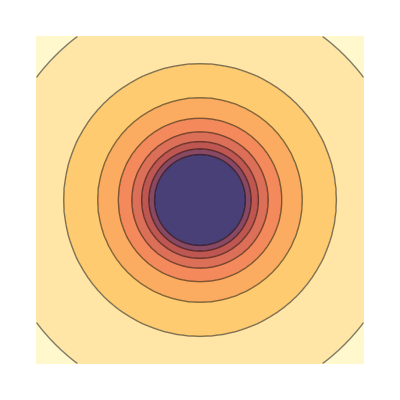
Single-Body Gravitational Potential
-Graphics-

```mathematica
plotSingle = Framed[
			Column[
			{
			Style["Single-Body Gravitational Potential",Bold,16],
			GraphicsRow[
			{
			Plot3D[gravPotential[1, 1, 1, 0, 0, x, y], {x, -4, 4}, {y, -4, 4},Axes->False],
			ContourPlot[gravPotential[1, 1, 1, 0, 0, x, y], {x, -4, 4}, {y, -4, 4}, ClippingStyle->Automatic,Frame->False]
			}
			]
			},
			Alignment->Center],
			FrameMargins->10]
```

### Two-Body Gravitational Potential

Single-body potentials are additive, so to make the potential for two bodies all we need to do is add them together. 
You’ll notice I’ve done a few things to make working with this data easier:

I’ve set m and G to be 1. I only really care about the general shape of the potential, which these won’t impact.

I’ve constrained the system to lie along the X-axis by setting Y to zero.

I’ve constrained the system such that its center of mass is at the origin by setting M1 to position X1 and M2 to position -M1/M2X1. In general, two bodies will mutually orbit around their center of mass, and thus this is the point about which we will need to consider the centrifugal force. I think it makes things easier to visualize if we keep this right in the middle, although it does mean the objects change their separation when we play with their relative masses.

```mathematica
m=1;
g=1;
twoGrav[M1_, M2_, X1_, x_, y_]:=gravPotential[M1, m, g, X1, 0, x, y] + gravPotential[M2, m, g, -M1/M2 X1, 0, x,  y]
```

In the image below, you can see an equilibrium point between the two masses, where an object will feel an equal pull towards both objects.

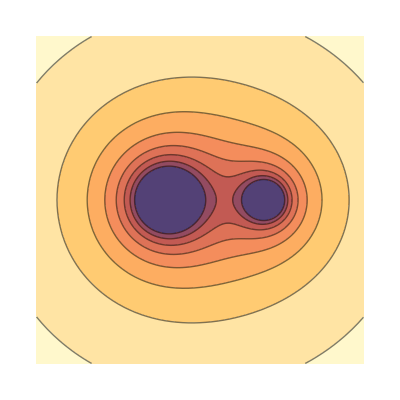
Two-Body Gravitational Potential
-Graphics-

```mathematica
plotDouble = Framed[
			Column[
			{
			Style["Two-Body Gravitational Potential",Bold,16],
			GraphicsRow[
			{
			Plot3D[twoGrav[2,1, -1, x, y], {x, -5,5}, {y, -5, 5}, PlotPoints->25,Axes->False],
			ContourPlot[twoGrav[2,1, -1, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->3,Frame->False]
			}
			]
			},
			Alignment->Center],
			FrameMargins->10]
```

Next, we tackle the “centrifugal potential”. The physics of this potential is rather nuanced, and but because we are going for intuitive here, I’m not going to spend much time on this point, but you can read a little more here if you are interested.
-Graphics-
MrRuebezahl via Reddit

If you have a ball on a string which you spin in a circle over your head, the ball traces a circular path, and your hand feels a force as though somebody is trying to pull the ball radially away from you. If you change the length of the string while rotating at the same rate, this force changes. 
In our space-based scenario, the two bodies we generate will be circling (i.e. orbiting) around their center of mass. I don’t want generate spinning plots, so we will pretend that the axes of the plots are spinning in lock-step with them. In physics, we’d call this a “rotating reference frame”. The important thing to realize is that objects in orbit experience the same kind of centrifugal potential as in our ball-on-a-rope example above, only instead of a rope they have the force of gravity keeping them bound to the system.

Note: In reality, the rotation rate “w” of the system is dependant on the mass and orbits of our two objects. However, I think it is easier for visualization if we pretend it is some independent thing we can turn on and off.

```mathematica
centrifugal[w_,m_,x_, y_]:= -1/2 w^2*m*EuclideanDistance[{0,0},{x,y}]^2
```

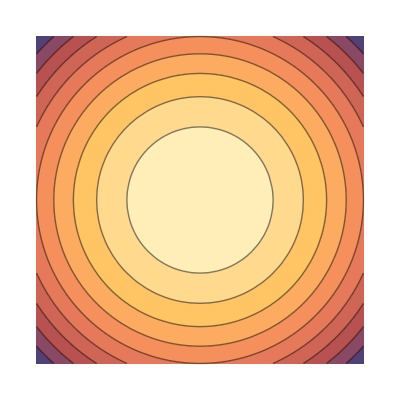
Centrifugal Potential
-Graphics-

```mathematica
plotCentri = Framed[
			Column[
			{
			Style["Centrifugal Potential",Bold,16],
			GraphicsRow[
			{
			Plot3D[centrifugal[1, m, x, y],{x,-5,5},{y,-5,5},Axes->False],
			ContourPlot[centrifugal[1, m, x, y],{x,-5,5},{y,-5,5},Frame->False]
			}
			]
			},
			Alignment->Center],
			FrameMargins->10]
```

### Effective Potential

Just as we could examine the gravitational potential of two masses by adding their individual potentials together, we can do the same with our centrifugal potential.

```mathematica
effectivePotential[m_,spin_,ratio_,separation_,x_,y_]:=twoGrav[ratio*m,m, -separation, x, y]+centrifugal[spin,1, x, y]
```

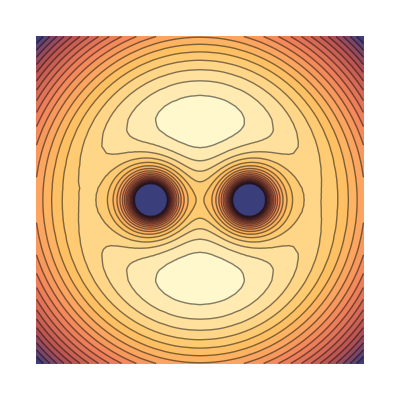
Effective Potential
-Graphics-

```mathematica
plotEffective= Framed[
				Column[
				{
				Style["Effective Potential",Bold,16],
				GraphicsRow[
				{
				Plot3D[effectivePotential[1,0.3,1,1.5,x,y], {x, -5, 5}, {y, -5, 5}, 
				ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, Axes->False],
				ContourPlot[effectivePotential[1,0.3,1,1.5,x,y], {x, -5, 5}, {y, -5, 5}, 
				ClippingStyle->Automatic, MaxRecursion->2, Contours->20, Frame->False]
				}
				]
				},
				Alignment->Center],
				FrameMargins->10]
```

## The Lagrange Points

If we imagine this effective potential as a physical surface, the Lagrange points exist at the locations you could place a marble and have it stay perfectly still. To actually plot these points, we need to do a little bit of math. Namely, recall that the force an object feels is equal and opposite to the change in its potential energy (U). Also, recall that force is a vector (it has a magnitude and a direction), where potential energy is a scaler (it has a magnitude, but on direction).

F = -∇U

```mathematica
$Assumptions= x∈Reals && y∈Reals;
force[m_,spin_,ratio_,separation_,x_,y_]:=FunctionExpand[-Grad[effectivePotential[m,spin,ratio,separation,x,y],{x,y}]]
```

The lines in the plot below represent how our hypothetical marble would fall if we placed it at a given point on the surface.

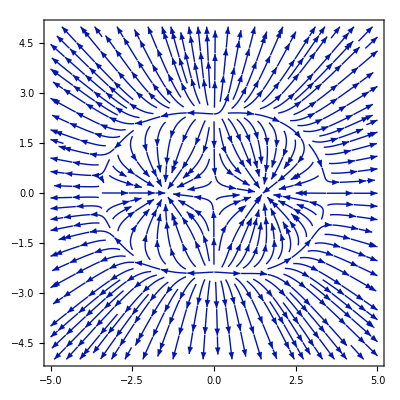

```mathematica
StreamPlot[
Evaluate@force[1,0.3,1,1.5,x,y],
{x,-5,5},{y,-5,5},
StreamPoints->Fine]
```

Mathematically, the Lagrange points exist where the force is zero . We can put this all together to visualize our final system, with the Lagrange points in red.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

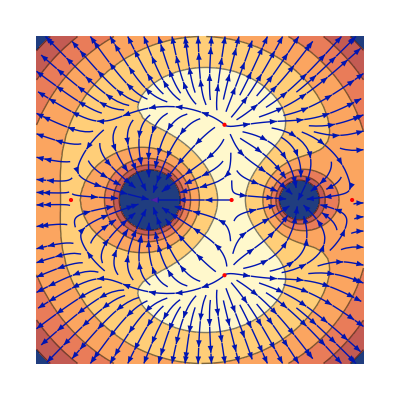
Lagrange Points
-Graphics-

```mathematica
m=1;
spin=0.3;
ratio=2;
separation=1.5;
lagrangePoints:=Solve[force[m,spin,ratio,separation,x,y]==0,{x,y}];

plotLagrange=Framed[
			Column[
			{
			Style["Lagrange Points",Bold,16],
			GraphicsRow[
			{
			Plot3D[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
			ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, Axes->False],
			Show[
			{
			ContourPlot[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
			ClippingStyle->Automatic, MaxRecursion->2, Contours->5, Frame->False],
			StreamPlot[
			Evaluate@force[m,spin,ratio,separation,x,y],
			{x,-5,5},{y,-5,5},
			StreamPoints->Automatic],
			Graphics[{Red,PointSize[Large],Point[{x,y}/. lagrangePoints]}]
			}]
			}
			]
			},
			Alignment->Center],
			FrameMargins->10]
```

## Try it Yourself!

In the object below, you can manually change the relevant parameters of the system to get an intuitive understanding of where the Lagrange points lie. I personally get the most use of this by slowly changing the spin of the system, and observing how the centrifugal force causes L4 and L5 to pop into existence when it gets strong enough.

```mathematica
manipAll = Manipulate[
			GraphicsColumn[
			{
			GraphicsRow[
			{
			Plot3D[twoGrav[ratio*m,m, -separation, x, y],{x, -5, 5}, {y, -5, 5}, 
			Mesh->None, 
			PlotLabel->"Gravitational Potential",Axes->False],
			Plot3D[centrifugal[spin, m, x, y], {x, -5, 5}, {y, -5, 5}, 
			Mesh->None, 
			PlotLabel->"Centrifugal Potential",Axes->False]
			}
			],
			GraphicsRow[
			{
			Plot3D[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
			ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, 
			PlotLabel->"Effective Potential",Axes->False],
			ContourPlot[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
			ClippingStyle->Automatic, MaxRecursion->2, Contours->5, 
			PlotLabel->"Effective Potential",Frame->False]
			}
			]
			}
			],
			{{spin,0.3},0,1},{{separation,1.5},0,3},{{ratio,2},1,3}]
```

## Making Graphics for Export

### Static Images

```mathematica
Export["singleObject.jpg",plotSingle,"CompressionLevel"->0];
Export["doubleObject.jpg",plotDouble,"CompressionLevel"->0];
Export["centrifugalPotential.jpg",plotCentri,"CompressionLevel"->0];
Export["effectivePotential.jpg",plotEffective,"CompressionLevel"->0];
Export["lagrangePoints.jpg", plotLagrange, "CompressionLevel"->0];
```

### Gifs

```mathematica
Export["spin.gif",Table[
					Framed[
					Column[
					{
					Style["Effective Potential",Bold,16],
					GraphicsRow[
					{
					Plot3D[effectivePotential[1,spin,1,0,x,y], {x, -5, 5}, {y, -5, 5}, 
					ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, Axes->False],
					ContourPlot[effectivePotential[1,spin,1,0,x,y], {x, -5, 5}, {y, -5, 5}, 
					ClippingStyle->Automatic, MaxRecursion->2, Contours->20, Frame->False]
					}
					]
					},
					Alignment->Center],
					FrameMargins->10],
					{spin,0,0.3,0.005}
					]
					]
```

spin.gif

```mathematica
Export["separation.gif",Table[
						Framed[
						Column[
						{
						Style["Effective Potential",Bold,16],
						GraphicsRow[
						{
						Plot3D[effectivePotential[1,0.3,1,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
						ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, Axes->False],
						ContourPlot[effectivePotential[1,0.3,1,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
						ClippingStyle->Automatic, MaxRecursion->2, Contours->20, Frame->False]
						}
						]
						},
						Alignment->Center],
						FrameMargins->10],
						{separation,0,1.5,0.05}
						]
						]
```

separation.gif

```mathematica
Export["ratio.gif",Table[
						Framed[
						Column[
						{
						Style["Effective Potential",Bold,16],
						GraphicsRow[
						{
						Plot3D[effectivePotential[1,0.3,ratio,1.5,x,y], {x, -5, 5}, {y, -5, 5}, 
						ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, Axes->False],
						ContourPlot[effectivePotential[1,0.3,ratio,1.5,x,y], {x, -5, 5}, {y, -5, 5}, 
						ClippingStyle->Automatic, MaxRecursion->2, Contours->20, Frame->False]
						}
						]
						},
						Alignment->Center],
						FrameMargins->10],
						{ratio,1,2,0.05}
						]
						]
```

ratio.gif

```mathematica
Export["manipulate.gif", manipAll]
```

manipulate.gif